## Лабораторная работа №5 Калиновский Владимир, ПО-4

```mathematica
Задание 1. Арифметические вычисления
```

```mathematica
Пробел выполняет роль знака умножния:
```

```mathematica
3 5 (*пробел автоматически ставит умножение*)
```

15

```mathematica
Введение дополнительных пробелов не изменяют результата вычислений:
```

```mathematica
3      5
```

15

```mathematica
2+   7
```

9

```mathematica
3      /7
```

3/7

```mathematica
Целые, рациональные и иррациональные числа считаются заданными точно. Поэтому в выражениях, содержащих только такие числа, при обработке производятся лишь возможные упрощения, но сами они остаются точными и преобразуются в числа, заданные приближенно, только по команде пользователя. (*рациональные - обыкновенные дроби*)
```

```mathematica
17^(1/2)
```

√17

```mathematica
2/3
```

2/3

```mathematica
Действительные числа, содержащие десятичную точку, считаются заданными приближенно. Поэтому выражения, в которые входят действительные числа, вычисляются при обработке секции без специальной команды. (*действительные - все положительные, отрицательные и ноль*)
```

```mathematica
17.^(1/2)
```

4.12311

```mathematica
Для изменения стандартного порядка выполнения операций используются скобки
```

```mathematica
7 (1 + 2)
```

21

```mathematica
Задание 2.
```

```mathematica
N[Sqrt[17], 200]
```

4.1231056256176605498214098559740770251471992253736204343986335730949543463376215935878636508106842966845440409392141416153014208404158683630795481457469069776770232664362408630877905675723857082255214

```mathematica
Precision[%] 
(*точность вычисления*)
(*% - ссылка на предыдущий результат. %% - предпоследний и т.д.*)
```

200.

```mathematica
N[Sqrt[17]]
```

4.12311

```mathematica
Sqrt[17]
```

√17

```mathematica
var1 = N[E^(Pi*Sqrt[163]), 40]
var2 = Round[var1]
var2 - var1
```

2.625374126407687439999999999992500725972×10^17

262537412640768744

7.499274028×10^-13

```mathematica
(10*((10.8*10^3)/300)^(1/2)+4)^(1/3)
```

4.

```mathematica
(10^-24*10^12)/10^-14 √(32768/2^9)
```

800

```mathematica
5>3
5<2
```

True

False

```mathematica
Pi^E>E^Pi
```

False

```mathematica
N[Pi^E]
N[E^Pi]
```

22.4592

23.1407

```mathematica
Задание 3. Численное решение уравнений
-Graphics-
```

```mathematica
NSolve[√(x+2)+4*x == 4, x]
NSolve[x^3-3*x^2+5== 0, x]
```

{{x→0.597111}}

{{x→-1.1038},{x→2.0519-0.565236 ⅈ},{x→2.0519+0.565236 ⅈ}}

```mathematica
NSolve[{x^2+x*y+y^2==1, x^3+x^2*y+x*y^2+y^3==4}, {x,y}]
```

{{x→-1.-1.41421 ⅈ,y→-1.+1.41421 ⅈ},{x→-1.+1.41421 ⅈ,y→-1.-1.41421 ⅈ},{x→1.6838+0.133552 ⅈ,y→-0.683802-1.13355 ⅈ},{x→1.6838-0.133552 ⅈ,y→-0.683802+1.13355 ⅈ},{x→-0.683802-1.13355 ⅈ,y→1.6838+0.133552 ⅈ},{x→-0.683802+1.13355 ⅈ,y→1.6838-0.133552 ⅈ}}

```mathematica
NSolve[{x-y^2+3*z ==34, x+y-z==-1, -x+2*y+3*z ==4}, {x,y,z}]
```

{{x→9.25-10.2317 ⅈ,y→-3.5+4.09268 ⅈ,z→6.75-6.13901 ⅈ},{x→9.25+10.2317 ⅈ,y→-3.5-4.09268 ⅈ,z→6.75+6.13901 ⅈ}}

```mathematica
NSolve[{x^3+y^2+7*x^2*y+4*y^2*x==72,x+7*y==22}, {x,y}]
```

```mathematica
{{x->-223.61958236920438,y->35.088511767029196},{x->1.0649955671154616,y->2.9907149189835054},{x->-3.1954131980035045,y->3.599344742571929}}
```

```mathematica
Задание 4. Вариант 11
```

```mathematica
(*The algebraic methods available in NSolve cannot handle general equations with transcendental functions, FindRoot finds one root*)
-Graphics-
```

```mathematica
FindRoot[2*Sin[x]+1 == x^2-2*x-3, {x, 4}]
```

{x→3.20675}

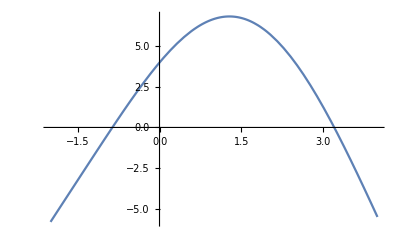

```mathematica
Plot[{2*Sin[x]+1 == x^2-2*x-3}, {x, -2,4}]
```

```mathematica
Задание 5. Численное решение дифференциальных уравнений
```

```mathematica
func1=NDSolve[{y''[x]+ Cos[x]*y'[x]-x^2==0, y[0]==0, y'[0]==2},y, {x,-5,2}]
```

{{y→InterpolatingFunction[…]}}

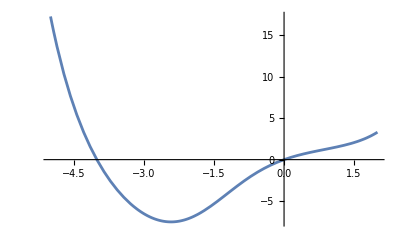

```mathematica
Plot[y[x]/.func1, {x,-5,2}, 
PlotStyle->{Thickness[0.005]}]
```

```mathematica
func2=FindRoot[(y[x]/.func1)==0, {x,-4}]
func22=FindRoot[(y[x]/.func1)==0, {x,0}]
```

{x→-4.00784}

{x→0.}

```mathematica
D[y[x]/.func1,x]/.func2
D[y[x]/.func1,x]/.func22
```

{-10.1787}

{2.}

```mathematica
func3 = FindRoot[D[y[x]/.func1,x]==0, {x,-2.6}]
(*локальный минимум*)
```

{x→-2.41946}

```mathematica
y[x]/.func1/.func3
```

{-7.4998}

```mathematica
FindMinimum[y[x]/.func1[[1]], {x,-2.6}]
```

{-7.4998,{x→-2.41946}}

```mathematica
Задание 6. Обработка численных данных
```

```mathematica
var4=Table[{x,(7+3*x+1*x^2+2*x^3+9*x^4)(1+Random[Real,{-0.5,0.5}])},{x,-1,6,0.5}]
```

{{-1.,12.0552},{-0.5,5.53147},{0.,8.21171},{0.5,12.6299},{1.,27.224},{1.5,90.4797},{2.,91.2084},{2.5,264.938},{3.,919.203},{3.5,1556.95},{4.,3405.55},{4.5,3792.35},{5.,6546.66},{5.5,11184.},{6.,16287.5}}

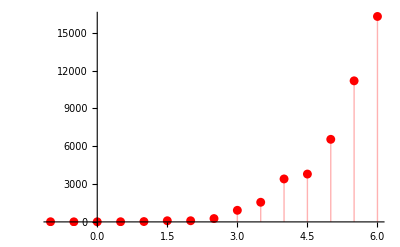

```mathematica
graph1=ListPlot[var4,PlotStyle->{PointSize[0.016],Red},Filling->Axis]
```

```mathematica
-Graphics-
-Graphics- -Graphics- 
(*Fit is typically used for fitting combinations of functions to data,including polynomials and exponentials.It provides one of the simplest ways to get a model from data.*)
```

```mathematica
apr1=Fit[var4,{1,x,x^2,x^3,x^4},x]
```

-106.615+76.7484 x+170.195 x^2-107.396 x^3+25.4542 x^4

```mathematica
apr2=Fit[var4,{1,x,Sin[x]},x](*экспериментальные точки*)
```

-731.967+1178.56 x-1059.77 Sin[x]

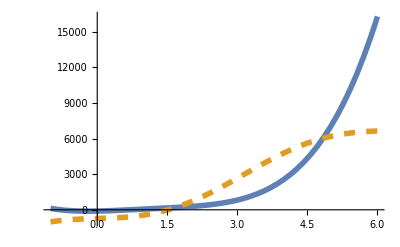

```mathematica
y1=Plot[{apr1,apr2},{x,-1,6},
PlotStyle->{{Thickness[0.01]},{Thickness[0.01],Dashing[{0.02}]}}]
```

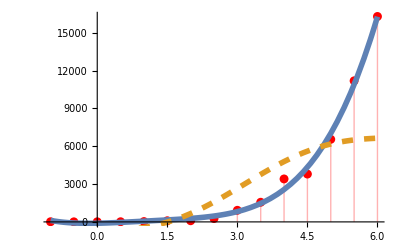

```mathematica
Show[graph1,y1]
```